```mathematica
Clear[ρ,P]
```

```mathematica
Clear[coord,metric,inversemetric,affine,riemann,ricci,scalar,einstein,r,θ,ϕ,t]
```

```mathematica
n=4
```

4

```mathematica
coord={t,r,θ,ϕ}
```

{t,r,θ,ϕ}

```mathematica
metric={{-1,0,0,0},{0,a[t]^2/(1-K*r^2),0,0},{0,0,a[t]^2*r^2,0},{0,0,0,a[t]^2*r^2 Sin[θ]^2}}
```

{{-1,0,0,0},{0,a[t]^2/(1-K r^2),0,0},{0,0,r^2 a[t]^2,0},{0,0,0,r^2 a[t]^2 Sin[θ]^2}}

```mathematica
metric//MatrixForm
```

(-1 | 0 | 0 | 0
0 | a[t]^2/(1-K r^2) | 0 | 0
0 | 0 | r^2 a[t]^2 | 0
0 | 0 | 0 | r^2 a[t]^2 Sin[θ]^2)

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{-1,0,0,0},{0,(1-K r^2)/a[t]^2,0,0},{0,0,1/(r^2 a[t]^2),0},{0,0,0,Csc[θ]^2/(r^2 a[t]^2)}}

```mathematica
inversemetric//MatrixForm
```

(-1 | 0 | 0 | 0
0 | (1-K r^2)/a[t]^2 | 0 | 0
0 | 0 | 1/(r^2 a[t]^2) | 0
0 | 0 | 0 | Csc[θ]^2/(r^2 a[t]^2))

```mathematica
affine:=affine=Simplify[Table[0.5*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[affine[[i,j,k]]=!=0,{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | 0.
Γ[1, 2, 1] | 0.
Γ[1, 2, 2] | -(1. a[t] a'[t])/(-1.+K r^2)
Γ[1, 3, 1] | 0.
Γ[1, 3, 2] | 0.
Γ[1, 3, 3] | 1. r^2 a[t] a'[t]
Γ[1, 4, 1] | 0.
Γ[1, 4, 2] | 0.
Γ[1, 4, 3] | 0.
Γ[1, 4, 4] | 1. r^2 a[t] Sin[θ]^2 a'[t]
Γ[2, 1, 1] | 0.
Γ[2, 2, 1] | (1. a'[t])/a[t]
Γ[2, 2, 2] | -(1. K r)/(-1.+K r^2)
Γ[2, 3, 1] | 0.
Γ[2, 3, 2] | 0.
Γ[2, 3, 3] | 1. r (-1.+K r^2)
Γ[2, 4, 1] | 0.
Γ[2, 4, 2] | 0.
Γ[2, 4, 3] | 0.
Γ[2, 4, 4] | 1. r (-1.+K r^2) Sin[θ]^2
Γ[3, 1, 1] | 0.
Γ[3, 2, 1] | 0.
Γ[3, 2, 2] | 0.
Γ[3, 3, 1] | (1. a'[t])/a[t]
Γ[3, 3, 2] | 1./r
Γ[3, 3, 3] | 0.
Γ[3, 4, 1] | 0.
Γ[3, 4, 2] | 0.
Γ[3, 4, 3] | 0.
Γ[3, 4, 4] | -1. Cos[θ] Sin[θ]
Γ[4, 1, 1] | 0.
Γ[4, 2, 1] | 0.
Γ[4, 2, 2] | 0.
Γ[4, 3, 1] | 0.
Γ[4, 3, 2] | 0.
Γ[4, 3, 3] | 0.
Γ[4, 4, 1] | (1. a'[t])/a[t]
Γ[4, 4, 2] | 1./r
Γ[4, 4, 3] | 1. Cot[θ]
Γ[4, 4, 4] | 0.

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]*affine[[i,k,s]]-affine[[s,j,k]]*affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 1, 2, 1] | 0.
R[1, 1, 3, 1] | 0.
R[1, 1, 3, 2] | 0.
R[1, 1, 4, 1] | 0.
R[1, 1, 4, 2] | 0.
R[1, 1, 4, 3] | 0.
R[1, 2, 2, 1] | 0.+(1. a[t] a''[t])/(-1.+K r^2)
R[1, 2, 3, 1] | 0.
R[1, 2, 3, 2] | 0.
R[1, 2, 4, 1] | 0.
R[1, 2, 4, 2] | 0.
R[1, 2, 4, 3] | 0.
R[1, 3, 2, 1] | 0.
R[1, 3, 3, 1] | 0.-1. r^2 a[t] a''[t]
R[1, 3, 3, 2] | 0.
R[1, 3, 4, 1] | 0.
R[1, 3, 4, 2] | 0.
R[1, 3, 4, 3] | 0.
R[1, 4, 2, 1] | 0.
R[1, 4, 3, 1] | 0.
R[1, 4, 3, 2] | 0.
R[1, 4, 4, 1] | -1. r^2 a[t] Sin[θ]^2 a''[t]
R[1, 4, 4, 2] | 0.
R[1, 4, 4, 3] | 0.
R[2, 1, 2, 1] | 0.-(1. a''[t])/a[t]
R[2, 1, 3, 1] | 0.
R[2, 1, 3, 2] | 0.
R[2, 1, 4, 1] | 0.
R[2, 1, 4, 2] | 0.
R[2, 1, 4, 3] | 0.
R[2, 2, 2, 1] | 0.
R[2, 2, 3, 1] | 0.
R[2, 2, 3, 2] | 0.
R[2, 2, 4, 1] | 0.
R[2, 2, 4, 2] | 0.
R[2, 2, 4, 3] | 0.
R[2, 3, 2, 1] | 0.
R[2, 3, 3, 1] | 0.
R[2, 3, 3, 2] | 0.-1. K r^2-1. r^2 a'[t]^2
R[2, 3, 4, 1] | 0.
R[2, 3, 4, 2] | 0.
R[2, 3, 4, 3] | 0.
R[2, 4, 2, 1] | 0.
R[2, 4, 3, 1] | 0.
R[2, 4, 3, 2] | 0.
R[2, 4, 4, 1] | 0.
R[2, 4, 4, 2] | r^2 Sin[θ]^2 (-1. K-1. a'[t]^2)
R[2, 4, 4, 3] | 0.
R[3, 1, 2, 1] | 0.
R[3, 1, 3, 1] | 0.-(1. a''[t])/a[t]
R[3, 1, 3, 2] | 0.
R[3, 1, 4, 1] | 0.
R[3, 1, 4, 2] | 0.
R[3, 1, 4, 3] | 0.
R[3, 2, 2, 1] | 0.
R[3, 2, 3, 1] | 0.
R[3, 2, 3, 2] | 0.-(1. K)/(-1.+K r^2)-(1. a'[t]^2)/(-1.+K r^2)
R[3, 2, 4, 1] | 0.
R[3, 2, 4, 2] | 0.
R[3, 2, 4, 3] | 0.
R[3, 3, 2, 1] | 0.
R[3, 3, 3, 1] | 0.
R[3, 3, 3, 2] | 0.
R[3, 3, 4, 1] | 0.
R[3, 3, 4, 2] | 0.
R[3, 3, 4, 3] | 0.
R[3, 4, 2, 1] | 0.
R[3, 4, 3, 1] | 0.
R[3, 4, 3, 2] | 0.
R[3, 4, 4, 1] | 0.
R[3, 4, 4, 2] | 0.
R[3, 4, 4, 3] | r^2 Sin[θ]^2 (-1. K-1. a'[t]^2)
R[4, 1, 2, 1] | 0.
R[4, 1, 3, 1] | 0.
R[4, 1, 3, 2] | 0.
R[4, 1, 4, 1] | 0.-(1. a''[t])/a[t]
R[4, 1, 4, 2] | 0.
R[4, 1, 4, 3] | 0.
R[4, 2, 2, 1] | 0.
R[4, 2, 3, 1] | 0.
R[4, 2, 3, 2] | 0.
R[4, 2, 4, 1] | 0.
R[4, 2, 4, 2] | 0.-(1. K)/(-1.+K r^2)-(1. a'[t]^2)/(-1.+K r^2)
R[4, 2, 4, 3] | 0.
R[4, 3, 2, 1] | 0.
R[4, 3, 3, 1] | 0.
R[4, 3, 3, 2] | 0.
R[4, 3, 4, 1] | 0.
R[4, 3, 4, 2] | 0.
R[4, 3, 4, 3] | -1.+1. K r^2-1. Cot[θ]^2+1. Csc[θ]^2+1. r^2 a'[t]^2
R[4, 4, 2, 1] | 0.
R[4, 4, 3, 1] | 0.
R[4, 4, 3, 2] | 0.
R[4, 4, 4, 1] | 0.
R[4, 4, 4, 2] | 0.
R[4, 4, 4, 3] | 0.

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | 0.-(3. a''[t])/a[t]
R[2, 1] | 0.
R[2, 2] | 0.-(2. K)/(-1.+K r^2)-(2. a'[t]^2)/(-1.+K r^2)-(1. a[t] a''[t])/(-1.+K r^2)
R[3, 1] | 0.
R[3, 2] | 0.
R[3, 3] | -1.+2. K r^2-1. Cot[θ]^2+1. Csc[θ]^2+2. r^2 a'[t]^2+1. r^2 a[t] a''[t]
R[4, 1] | 0.
R[4, 2] | 0.
R[4, 3] | 0.
R[4, 4] | 2. r^2 Sin[θ]^2 (1. K+1. a'[t]^2+0.5 a[t] a''[t])

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]*ricci[[i,j]],{i,1,n},{j,1,n}]]
```

(6. K+6. a'[t]^2+6. a[t] a''[t])/a[t]^2

```mathematica
einstein:=einstein=Simplify[ricci-0.5*scalar*metric]
```

```mathematica
listeinstein:=Table[If[UnsameQ[einstein[[j,l]],0],{ToString[G[j,l]],einstein[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listeinstein],Null],2],TableSpacing->{2,2}]
```

G[1, 1] | 0.+(3. K+3. a'[t]^2)/a[t]^2
G[2, 1] | 0.
G[2, 2] | 0.+(1. K)/(-1.+K r^2)+(1. a'[t]^2)/(-1.+K r^2)+(2. a[t] a''[t])/(-1.+K r^2)
G[3, 1] | 0.
G[3, 2] | 0.
G[3, 3] | -1.-1. K r^2-1. Cot[θ]^2+1. Csc[θ]^2-1. r^2 a'[t]^2-2. r^2 a[t] a''[t]
G[4, 1] | 0.
G[4, 2] | 0.
G[4, 3] | 0.
G[4, 4] | r^2 Sin[θ]^2 (-1. K-1. a'[t]^2-2. a[t] a''[t])

```mathematica
Subscript[G, 11]=(3*K+3*a'[t]^2)/a[t]^2==8*π*ρ[t]
```

(3 K+3 a'[t]^2)/a[t]^2==8 π ρ[t]

```mathematica
Subscript[G, 22]=((1* K)/(-1+K r^2)+a'[t]^2/(-1+K r^2)+(2* a[t] a''[t])/(-1+K r^2))==8*π*P[t]*a[t]^2/(1-K r^2)
```

K/(-1+K r^2)+a'[t]^2/(-1+K r^2)+(2 a[t] a''[t])/(-1+K r^2)==(8 π a[t]^2 P[t])/(1-K r^2)

```mathematica
Subscript[G, 33]=- K *r^2-r^2 *a'[t]^2-2 *r^2 *a[t]* a''[t]==8*π*P[t]*a[t]^2*r^2
```

-K r^2-r^2 a'[t]^2-2 r^2 a[t] a''[t]==8 π r^2 a[t]^2 P[t]

```mathematica
Subscript[G, 44]=- K *r^2-r^2 *a'[t]^2-2 *r^2 *a[t]* a''[t]==8*π*P[t]*a[t]^2*r^2*Sin[θ]^2
```

-K r^2-r^2 a'[t]^2-2 r^2 a[t] a''[t]==8 π r^2 a[t]^2 P[t] Sin[θ]^2

```mathematica
Subscript[G, 11]
```

(3 K+3 a'[t]^2)/a[t]^2==8 π ρ[t]

```mathematica
u={1,0,0,0}
```

{1,0,0,0}

```mathematica
T:=Simplify[(ρ[t]+P[t])* Outer[Times,u,u]+P[t] *inversemetric]
```

```mathematica
T
```

{{ρ[t],0,0,0},{0,((1-K r^2) P[t])/a[t]^2,0,0},{0,0,P[t]/(r^2 a[t]^2),0},{0,0,0,(Csc[θ]^2 P[t])/(r^2 a[t]^2)}}

```mathematica
T//MatrixForm
```

(ρ[t] | 0 | 0 | 0
0 | ((1-K r^2) P[t])/a[t]^2 | 0 | 0
0 | 0 | P[t]/(r^2 a[t]^2) | 0
0 | 0 | 0 | (Csc[θ]^2 P[t])/(r^2 a[t]^2))

```mathematica
T1=metric.T.metric
```

{{ρ[t],0,0,0},{0,(a[t]^2 P[t])/(1-K r^2),0,0},{0,0,r^2 a[t]^2 P[t],0},{0,0,0,r^2 a[t]^2 P[t] Sin[θ]^2}}

```mathematica
T1//MatrixForm
```

(ρ[t] | 0 | 0 | 0
0 | (a[t]^2 P[t])/(1-K r^2) | 0 | 0
0 | 0 | r^2 a[t]^2 P[t] | 0
0 | 0 | 0 | r^2 a[t]^2 P[t] Sin[θ]^2)

```mathematica
covariantT:=Simplify[Table[D[T[[i,ν]],coord[[ν]]]+Sum[affine[[i,ν,s]] T[[s,ν]]+affine[[ν,ν,s]] T[[i,s]],{s,1,n}],{i,1,n},{ν,1,n}]]
```

```mathematica
covariantT//TableForm
```

0.+ρ'[t] | 0.+((1. P[t]+1. ρ[t]) a'[t])/a[t] | 0.+((1. P[t]+1. ρ[t]) a'[t])/a[t] | 0.+((1. P[t]+1. ρ[t]) a'[t])/a[t]
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.

```mathematica
covariantT=FullSimplify[covariantT]
```

{{0.+ρ'[t],0.+((1. P[t]+1. ρ[t]) a'[t])/a[t],0.+((1. P[t]+1. ρ[t]) a'[t])/a[t],0.+((1. P[t]+1. ρ[t]) a'[t])/a[t]},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}

```mathematica
NonZeroEntries=Total[Flatten[FullSimplify[covariantT]]]
```

0.+(3 (1. P[t]+1. ρ[t]) a'[t])/a[t]+ρ'[t]

```mathematica
ConsEqn=(3 (P[t]+ρ[t])* a'[t])/a[t]+ρ'[t]==0
```

(3 (P[t]+ρ[t]) a'[t])/a[t]+ρ'[t]==0

```mathematica
Solution1=Solve[Subscript[G, 11] , ρ[t]]
```

{{ρ[t]→(3 (K+a'[t]^2))/(8 π a[t]^2)}}

```mathematica
Solution1rhs=(3 *(K+a'[t]^2))/(8 *π *a[t]^2)
```

(3 (K+a'[t]^2))/(8 π a[t]^2)

```mathematica
Solution2=Solve[Subscript[G, 22],P[t]]
```

{{P[t]→(-K-a'[t]^2-2 a[t] a''[t])/(8 π a[t]^2)}}

```mathematica
{{P[t]->(-K-a'[t]^2-2 a[t] a''[t])/(8 π a[t]^2)}}
```

{{P[t]→(-K-a'[t]^2-2 a[t] a''[t])/(8 π a[t]^2)}}

```mathematica
EoS=P[t]==μ*ρ[t]
```

P[t]==μ ρ[t]

```mathematica
EoS=EoS/. {μ->0}
```

P[t]==0

```mathematica
ConsEqn=ConsEqn/.{P[t]->0}
```

(3 ρ[t] a'[t])/a[t]+ρ'[t]==0

```mathematica
ConsEqn1=ConsEqn/.{ρ[t]->Solution1rhs,ρ'[t]->D[Solution1rhs,t]}
```

(3 a'[t] (K+a'[t]^2))/(8 π a[t]^3)+(3 a'[t] a''[t])/(4 π a[t]^2)==0

```mathematica
Simplify[ConsEqn1]
```

(a'[t] (K+a'[t]^2+2 a[t] a''[t]))/a[t]==0

```mathematica
ConsEqn1=Simplify[ConsEqn1]/. {K->1}
```

(a'[t] (1+a'[t]^2+2 a[t] a''[t]))/a[t]==0

```mathematica
ConsEqn2=((3 a'[t]* (K+a'[t]))/(8 π a[t]^3)+(3 a''[t])/(8 π a[t]^2))==0 /.{K->0}
```

(3 a'[t]^2)/(8 π a[t]^3)+(3 a''[t])/(8 π a[t]^2)==0

```mathematica
ConsEqn3=(K *a'[t]+a'[t]^2+a[t]* a''[t])/a[t]==0/.{K->-1}
```

(-a'[t]+a'[t]^2+a[t] a''[t])/a[t]==0

```mathematica
Solution4=NDSolve[{(a'[t] *(1+a'[t]^2+2 *a[t]* a''[t]))/a[t]==0,a[0]==1,a'[0]==0.1},a[t],{t,0,1.76}]
```

{{a[t]→InterpolatingFunction[…][t]}}

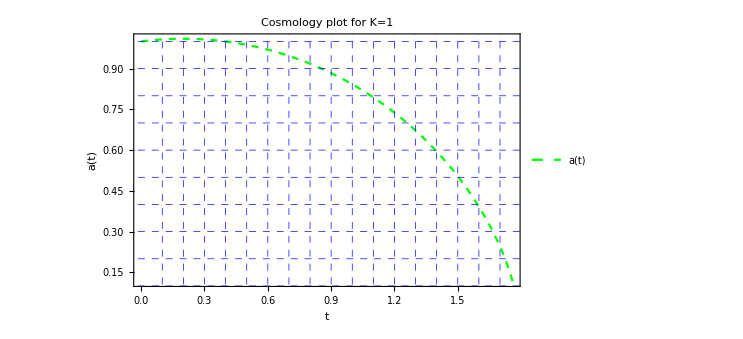

```mathematica
Plot[a[t]/. Solution4,{t,0,1.76},PlotStyle->{Green,Dashed},PlotLegends->Placed[LineLegend[{"a(t)"},LegendLayout->"Column",LegendFunction->"Panel"],{0.8,0.8}],Frame->True,FrameStyle->Directive[Brown,Thick],FrameLabel->{Style["t",Bold,30,Black],Style["a(t)",Bold,30,Black]},PlotLabel->Style["Cosmology plot for K=1",Bold,15,Red],LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->{Directive[Blue,17],(*Bottom ticks*)Directive[Red,17],(*Left ticks*)Directive[Brown,17],(*Top ticks*)Directive[Black,17]   (*Right ticks*)},FrameTicks->{(*Bottom ticks*){{0,0.2,0.4,0.6,0.8,1.0,1.2,1.4,1.6},None},(*Left ticks*){{0,0.3,0.6,0.8,1.0},None},(*Top ticks*){{0,0.2,0.4,0.6,0.8,1.0,1.2,1.4,1.6},None},(*Right ticks*){{0,0.3,0.6,0.8,1.0},None}},ImageSize->{550,350},GridLines->{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0,1.1,1.2,1.3,1.4,1.5,1.6,1.7},{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}},GridLinesStyle->Directive[Blue, Dashed]]
```

```mathematica
Solution5=NDSolve[{(3 a'[t]^2)/(8 π a[t]^3)+(3 a''[t])/(8 π a[t]^2)==0,a[0]==1,a'[0]==0.1},a[t],{t,0,15}]
```

{{a[t]→InterpolatingFunction[…][t]}}

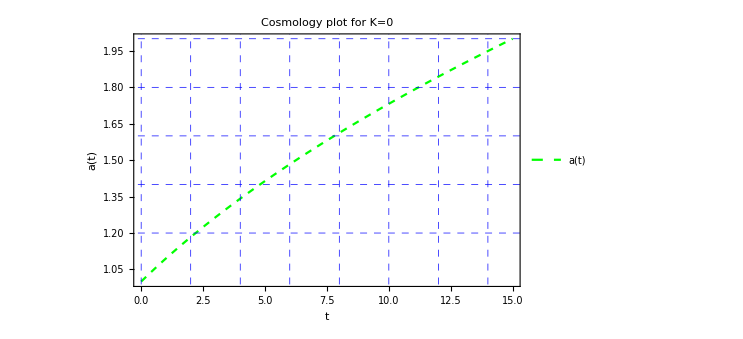

```mathematica
Plot[a[t]/. Solution5,{t,0,15},PlotStyle->{Green,Dashed},PlotLegends->Placed[LineLegend[{"a(t)"},LegendLayout->"Column",LegendFunction->"Panel"],{0.87,0.1}],Frame->True,FrameStyle->Directive[Brown,Thick],FrameLabel->{Style["t",Bold,30,Black],Style["a(t)",Bold,30,Black]},PlotLabel->Style["Cosmology plot for K=0",Bold,15,Red],LabelStyle->Directive[Bold,Black,20],FrameTicksStyle->{Directive[Blue,17],(*Bottom ticks*)Directive[Red,17],(*Left ticks*)Directive[Brown,17],(*Top ticks*)Directive[Black,17]},(*Right ticks*)FrameTicks->{(*Bottom ticks*){{0,2,4,6,8,10,12,14,16},None},(*Left ticks*){{0,1.2,1.4,1.6,1.8,2.0},None},(*Top ticks*){{0,2,4,6,8,10,12,14,16},None},(*Right ticks*){{0,1.2,1.4,1.6,1.8,2.0},None}},ImageSize->{550,350},GridLines->{{0,2,4,6,8,10,12,14,16},{0,1.2,1.4,1.6,1.8,2.0}},GridLinesStyle->Directive[Blue,Dashed]]
```

```mathematica
Solution6=NDSolve[{(-a'[t]+a'[t]^2+a[t] a''[t])/a[t]==0,a[0]==1,a'[0]==0.1},a[t],{t,0,15}]
```

{{a[t]→InterpolatingFunction[…][t]}}

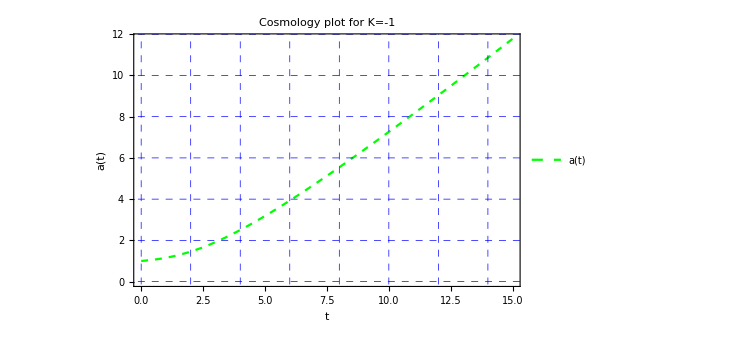

```mathematica
Plot[a[t]/. Solution6,{t,0,15},PlotStyle->{Green,Dashed},PlotLegends->Placed[LineLegend[{"a(t)"},LegendLayout->"Column",LegendFunction->"Panel",LabelStyle->{Bold,20}],{0.87,0.1}],Frame->True,FrameStyle->Directive[Brown,Thick],FrameLabel->{Style["t",Bold,30,Black],Style["a(t)",Bold,30,Black]},PlotLabel->Style["Cosmology plot for K=-1",Bold,20,Red],FrameTicksStyle->{Directive[Blue,17],(*Bottom ticks*)Directive[Red,17],(*Left ticks*)Directive[Brown,17],(*Top ticks*)Directive[Black,17]   (*Right ticks*)},FrameTicks->{{{0,2,4,6,8,10,12,14,16},None},(*Bottom ticks*){{0,2,4,6,8,10,12},None},(*Left ticks*){{0,2,4,6,8,10,12,14,16},None},(*Top ticks*){{0,2,4,6,8,10,12},None}            (*Right ticks*)},ImageSize->{550,350},GridLines->{{0,2,4,6,8,10,12,14,16},{0,2,4,6,8,10,12}},GridLinesStyle->Directive[Blue,Dashed]]
```